```mathematica
(*Import the dUdL for GibbsBog/4_longRun_4.8_2_3_v1v2, integrate it and determine the MVT L value*)
```

```mathematica
SetDirectory["/Volumes/MicroSD/Dropbox/PostDoc_SD/ZrC/Thermodynamic_Integration_Analysis/GibbsBog/4_longRun_4.8_2_3_v1v2"];
dudlFiles={"T_all_vol_dUdL"}
(*Data format, col1=L, col2=vol1, col2=vol2...*)
dudlDat=Table[ReadList[dudlFiles[[i]],{Number, Number,Number,Number,Number,Number}],{i,1,1}];
```

{T_all_vol_dUdL}

```mathematica
dudlV1=Partition[Transpose[{Transpose[dudlDat[[1]]][[1]],Transpose[dudlDat[[1]]][[2]]}],11]
```

{{{0.,1.30044},{0.1,1.20535},{0.2,1.1034},{0.3,1.05006},{0.4,0.956028},{0.5,0.901775},{0.6,0.837887},{0.7,0.705765},{0.8,0.647412},{0.9,0.577155},{1.,0.481672}},{{0.,3.60806},{0.1,3.09093},{0.2,2.82087},{0.3,2.38842},{0.4,2.09613},{0.5,1.78313},{0.6,1.49933},{0.7,1.14143},{0.8,0.744705},{0.9,0.502264},{1.,0.224474}},{{0.,11.3683},{0.1,9.02112},{0.2,7.2125},{0.3,5.51532},{0.4,4.17079},{0.5,2.81393},{0.6,1.33602},{0.7,-0.204451},{0.8,-1.43684},{0.9,-2.89021},{1.,-4.73043}},{{0.,17.6905},{0.1,12.4532},{0.2,9.72083},{0.3,6.98799},{0.4,4.26772},{0.5,1.90793},{0.6,-0.677226},{0.7,-2.69468},{0.8,-4.68569},{0.9,-7.4606},{1.,-9.1191}},{{0.,25.2679},{0.1,18.3906},{0.2,12.144},{0.3,8.10234},{0.4,3.88404},{0.5,0.384993},{0.6,-3.86393},{0.7,-7.10867},{0.8,-11.6086},{0.9,-15.5202},{1.,-21.0772}},{{0.,35.4395},{0.1,23.1089},{0.2,16.0527},{0.3,9.63508},{0.4,1.00689},{0.5,-2.81998},{0.6,-7.02322},{0.7,-15.6576},{0.8,-19.3586},{0.9,-25.8467},{1.,-32.3741}}}

```mathematica
dudlAll=Table[Partition[Transpose[{Transpose[dudlDat[[1]]][[1]],Transpose[dudlDat[[1]]][[1+vol]]}],11],{vol,1,5}];
```

```mathematica
dudlAllFit=Table[Table[Fit[dudlAll[[vol]][[temp]],{L^3,L^2,L,1},L],{temp,1,6,1}],{vol,1,5}];
dudlAllFitD=Table[Table[Fit[dudlAll[[vol]][[temp]],{L^3,L^2,L,1},L],{temp,1,6,1}],{vol,1,5}]
```

{{1.29499-0.927886 L+0.343986 L^2-0.231036 L^3,3.56705-4.16846 L+1.43031 L^2-0.63403 L^3,11.2946-23.3064 L+17.0081 L^2-9.70609 L^3,17.2299-42.9006 L+31.0216 L^2-14.7496 L^3,25.1469-74.3413 L+68.1317 L^2-40.0167 L^3,34.7011-110.971 L+95.5738 L^2-51.9566 L^3},{1.0476-1.55451 L+1.51867 L^2-0.877423 L^3,3.82258-5.08752 L+2.18813 L^2-0.686315 L^3,15.4182-28.6426 L+18.3969 L^2-7.31505 L^3,25.6878-60.8903 L+53.1834 L^2-24.1525 L^3,37.6657-96.786 L+90.4232 L^2-48.6126 L^3,55.1088-194.717 L+256.02 L^2-145.523 L^3},{0.745178-0.989482 L-0.470801 L^2+0.54093 L^3,3.62847-3.86541 L-1.10424 L^2+1.4349 L^3,17.9867-33.1795 L+24.6592 L^2-11.4787 L^3,29.7412-67.5245 L+59.2632 L^2-27.8964 L^3,46.6662-127.421 L+132.841 L^2-65.1994 L^3,62.1384-182.809 L+195.853 L^2-100.191 L^3},{0.213798-1.0308 L-0.192906 L^2+0.244377 L^3,3.90447-6.1358 L+2.9586 L^2-1.24855 L^3,23.712-54.8582 L+56.233 L^2-26.1439 L^3,36.2458-72.319 L+47.0166 L^2-14.8834 L^3,63.4379-201.559 L+260.379 L^2-135.122 L^3,87.1393-283.891 L+353.374 L^2-181.068 L^3},{-0.146285-1.53851 L+0.870624 L^2-0.445663 L^3,4.6903-8.9684 L+5.74673 L^2-2.24146 L^3,31.8599-73.9326 L+76.4101 L^2-35.6197 L^3,53.7233-146.409 L+173.792 L^2-86.2443 L^3,88.3608-282.714 L+366.783 L^2-187.329 L^3,128.874-486.899 L+714.166 L^2-389.998 L^3}}

```mathematica
bound1=0;bound2=1; mvtSolver[function_]:=Solve[Evaluate@function==(Integrate[Evaluate@function,{L,a,b}/.{a->bound1,b->bound2}]/(b-a)/.{a->bound1,b->bound2})&&L∈Interval[{0,1}],L,Reals]//N
dudlIntegrator[function_]:=NIntegrate[function,{L,bound1,bound2}]
```

```mathematica
mvtSolver[dudlAllFit[[1]][[1]]]
```

{{L→{0.500283}}}

```mathematica
(*print the MVT solver L value, the mid point L=0.5 dUdL value approximation to int dUdL, and the proper integrated value*)
midValintValMVT[fun_]:={mvtSolver[fun],
fun/.L->0.5,
dudlIntegrator[fun]}
midValintValMVT[dudlAllFit[[1]][[1]]]
```

{{{L→{0.500283}}},0.888161,0.887947}

```mathematica
(*vol1,temp*)


dudlOut=Table[Table[midValintValMVT[dudlAllFit[[vol]][[temp]]],{temp,1,6}]//TableForm,{vol,1,5}];
"MVT L, midpoint intval, intval"
dudlOut//TableForm
```

MVT L, midpoint intval, intval

L→{0.500283} | 0.888161 | 0.887947
L→{0.487596} | 1.76114 | 1.80108
L→{0.485013} | 2.6802 | 2.88428
L→{0.468097} | 1.69127 | 2.4327
L→{0.481434} | 0.00709288 | 0.682642
L→{0.473213} | -3.38545 | -1.91554
L→{0.475865} | 0.540333 | 0.557211
L→{0.47199} | 1.74007 | 1.83662
L→{0.461402} | 4.78175 | 5.40044
L→{0.447247} | 5.51949 | 6.93238
L→{0.46644} | 5.80187 | 7.26056
L→{0.438019} | 3.5649 | 6.70962
L→{0.473307} | 0.200353 | 0.228736
L→{0.477697} | 1.59907 | 1.68641
L→{0.464381} | 6.12687 | 6.74697
L→{0.451758} | 7.30774 | 8.75929
L→{0.436474} | 8.01611 | 10.9363
L→{0.44167} | 7.17317 | 10.9704
L→{0.486122} | -0.31928 | -0.304808
L→{0.478134} | 1.42015 | 1.51063
L→{0.427652} | 7.07317 | 8.49126
L→{0.445639} | 9.98007 | 12.0377
L→{0.4027} | 10.863 | 15.671
L→{0.4094} | 10.9039 | 17.7182
L→{0.48325} | -0.753591 | -0.736747
L→{0.460266} | 1.3626 | 1.56131
L→{0.426666} | 9.54366 | 11.4587
L→{0.41164} | 13.1865 | 16.8886
L→{0.394238} | 15.2836 | 22.4328
L→{0.376472} | 15.2164 | 25.9804

0.500283 | 0.487596 | 0.485013 | 0.468097 | 0.481434 | 0.473213
0.475865 | 0.47199 | 0.461402 | 0.447247 | 0.46644 | 0.438019
0.473307 | 0.477697 | 0.464381 | 0.451758 | 0.436474 | 0.44167
0.486122 | 0.478134 | 0.427652 | 0.445639 | 0.4027 | 0.4094
0.48325 | 0.460266 | 0.426666 | 0.41164 | 0.394238 | 0.376472

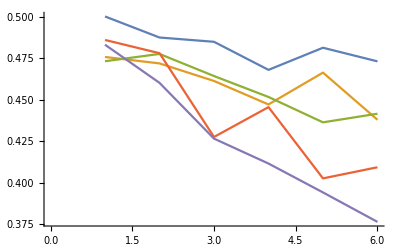

```mathematica
mvtOut=Table[Table[dudlOut[[vol]][[1]][[temp]][[1]][[1]][[1]][[2]][[1]],{temp,1,6}],{vol,1,5}];
mvtOut//TableForm
ListLinePlot[mvtOut]
```

```mathematica
3
```

```mathematica
"MVT L, midpoint intval, intval"
Table[midValintValMVT[dudlAllFit[[2]][[temp]]],{temp,1,6}]//TableForm
```

MVT L, midpoint intval, intval

L→0.475865
L→0.62748-0.883604 ⅈ
L→0.62748+0.883604 ⅈ | 0.540333 | 0.557211
L→0.47199
L→1.35812-2.07033 ⅈ
L→1.35812+2.07033 ⅈ | 1.74007 | 1.83662
L→0.461402
L→1.02677-1.3834 ⅈ
L→1.02677+1.3834 ⅈ | 4.78175 | 5.40044
L→0.447247
L→0.877367-0.983107 ⅈ
L→0.877367+0.983107 ⅈ | 5.51949 | 6.93238
L→0.46644
L→0.696818-0.924858 ⅈ
L→0.696818+0.924858 ⅈ | 5.80187 | 7.26056
L→0.438019
L→0.660649-0.568194 ⅈ
L→0.660649+0.568194 ⅈ | 3.5649 | 6.70962

```mathematica
"MVT L, midpoint intval, intval"
Table[midValintValMVT[dudlAllFit[[3]][[temp]]],{temp,1,6}]//TableForm
```

MVT L, midpoint intval, intval

L→-1.23555
L→0.473307
L→1.6326 | 0.200353 | 0.228736
L→-1.54362
L→0.477697
L→1.83548 | 1.59907 | 1.68641
L→0.464381
L→0.841939-1.18309 ⅈ
L→0.841939+1.18309 ⅈ | 6.12687 | 6.74697
L→0.451758
L→0.836322-0.982588 ⅈ
L→0.836322+0.982588 ⅈ | 7.30774 | 8.75929
L→0.436474
L→0.800494-0.784058 ⅈ
L→0.800494+0.784058 ⅈ | 8.01611 | 10.9363
L→0.44167
L→0.756563-0.764146 ⅈ
L→0.756563+0.764146 ⅈ | 7.17317 | 10.9704